# Liquid Crystal Laplacian By Jackson Burzynski, Raewyn Duvall, and Ben Nissan In this notebook we solve for the liquid crystal configuration in contact with a patterned surface. Effectively, solving this problem involves solving Laplace’s equation ∇^2 θ = 0 with the proper boundary conditions. To solve the Laplace equation, two different methods are used: Finite Difference and Finite Elements. We implement both algorithms and compare the energy in the LC configuration between both solutions and an analytical solution to the problem.

## Part I: Simplifying the Free Energy Expression We start by simplifying the free energy expression to prove that the minimizer is given by ∇^2 θ = 0

```mathematica
ClearAll[x,y,z,θ,ϕ]
```

First we define the director

```mathematica
n={Cos[θ[x,y]]Cos[ϕ],Cos[θ[x,y]]Sin[ϕ],Sin[θ[x,y]]};
```

```mathematica
(Div[n,{x,y,z}])^2+(n.Curl[n,{x,y,z}])^2+Cross[n,Curl[n,{x,y,z}]].Cross[n,Curl[n,{x,y,z}]]//Simplify
```

(θ^(0,1)[x,y])^2+(θ^(1,0)[x,y])^2

```mathematica
Grad[θ[x,y],{x,y,z}].Grad[θ[x,y],{x,y,z}]
```

(θ^(0,1)[x,y])^2+(θ^(1,0)[x,y])^2

Thus we have reduced the complicated free energy expression to (∇θ)^2

## Part II: The Finite Difference Approach Next we apply the method of Finite Differences to solve the Laplace Equation.

#### Define the Matrices

```mathematica
(* Function to construct the matrix and right hand side of our matrix equation *)
finiteDifferenceMatrices[nn_,xdim_,zdim_]:=Block[{M,P,Matrix,θ0},
(* Build the main Matrix *)
M=SparseArray[Join[
Table[{i,i}->1,{i,1,xdim}],(* boundary conditions *)
Table[{i,i}->1,{i,nn-xdim+1,nn}],
Table[{i,i}->-4,{i,xdim,nn-xdim}],(* diagonal *)
Table[{i,i+1}->1,{i,xdim+1,nn-xdim}],(* right neighbors *)
Table[{i,i-1}->1,{i,xdim+1,nn-xdim}],(* left neighbors *)
Table[{i,i-xdim}->1,{i,xdim+1,nn-xdim}], (* bottom neighbors *) 
Table[{i,i+xdim}->1,{i,xdim+1,nn-xdim}], (* top neighbors *)
Table[{i,i-1}->0,{i,xdim+1,nn-xdim,xdim}]
],{nn,nn}];
(* Build the matrix to handle periodic boundary conditions *)
P = SparseArray[Join[
Table[{i,i+xdim-1}->1,{i,xdim+1,nn-xdim,xdim}], (* left neighbor *)
Table[{i,i-1}->-1,{i,xdim+1,nn-xdim,xdim}],(* remove previous left neighbor *)
Table[{i,i-xdim+1}->1,{i,2*xdim,nn-xdim,xdim}],(* right neighbor *)
Table[{i,i+1}->-1,{i,2*xdim,nn-xdim,xdim}] (* remove previous right neighbor *)
],{nn,nn}];
(* Sum the matrices to obtain the correct matrix *)
Matrix = M+P;
(* Build the right hand side *)
θ0 = SparseArray[Join[
Table[{i,1}->Pi/2,{i,1,xdim/2}],
Table[{i,1}->Pi/2,{i,nn-xdim+1,nn-xdim/2}]
],{nn,1}];
Return[{Matrix,θ0}];]
```

```mathematica
(* Define the dimensions of our run *)
xdim = 20;
zdim = 20;
dims = xdim*zdim;
```

```mathematica
(* get the matrices *)
```

```mathematica
x=finiteDifferenceMatrices[dims,xdim,zdim]//N;
sol=Flatten[LinearSolve[x[[1]],x[[2]]]];
matrix = Partition[sol,xdim];
```

```mathematica
ListPlot3D[matrix]
```

-Graphics3D-

#### Calculate the Energy

We must calculate the integral F=1/2∫(∇θ)^2dV

```mathematica
(* Transform Matrix into list of 3-Tuples *)
grid[xdim_,zdim_] := Table[{N[x],N[z]},{z,0,1,1/(zdim)},{x,0,1,1/( xdim)}];
x=Flatten[grid[xdim-1,zdim-1],1];
```

```mathematica
theta =Map[Flatten,Transpose[{x,Flatten[matrix]}],1];
```

```mathematica
ListPlot3D[theta]
```

-Graphics3D-

```mathematica
(* Interpolate the data *)
```

```mathematica
interp=Interpolation[theta];
```

```mathematica
Plot3D[interp[x,z],{x,0,1},{z,0,1},PlotRange->All]
```

-Graphics3D-

```mathematica
(* Integrate to find the energy *)
```

```mathematica
der={D[interp[i,j],i],D[interp[i,j],j]}
```

{InterpolatingFunction[{{0., 1.}, {0., 1.}}, <>][i,j],InterpolatingFunction[{{0., 1.}, {0., 1.}}, <>][i,j]}

```mathematica
NIntegrate[der[x,z]*der[x,z],{x,0,1},{z,0,1}]
```

NIntegrate::inumr: The integrand « 1 »[x, z]^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1}, {0, 1}}.

NIntegrate[der[x,z] der[x,z],{x,0,1},{z,0,1}]

## Part III: The Finite Element Approach We now solve the same problem by using the method of Finite Elements

### The Mesh We begin by defining our computational mesh

```mathematica
grid[xdim_,zdim_] := Table[{N[x],N[z]},{z,0,1,1/(zdim)},{x,0,1,1/( xdim)}];
```

```mathematica
x=Flatten[grid[10,10],1];
```

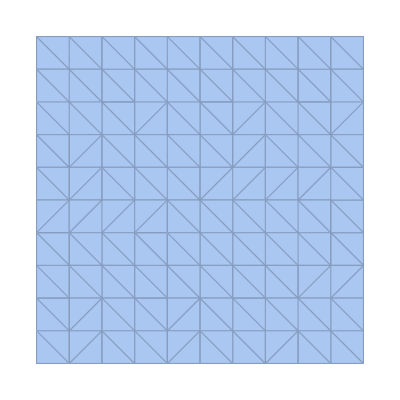

```mathematica
mesh = DelaunayMesh[x]
```

### Basis Functions We must define our basis functions v_n(x,z) to be 1 on the n^th grid point and 0 elsewhere

```mathematica
base[i_,j_,xdim_,zdim_] := Map[Flatten,Transpose[{Flatten[grid[xdim,zdim],1],Flatten[Table[If[{i,j}=={k,m},1,0],{k,xdim+1},{m,zdim+1}]]}]];
```

```mathematica
Manipulate[ListPlot3D[base[i,j,10,10]],{i,1,11,1},{j,1,11,1}]
```

```mathematica
ListPlot3D[base[5,5,10,10]]
```

-Graphics3D-

### The Inner Products We must define two matrices of inner products in order to calculate for the LC configuration L_ij=⟨∇v_i,∇v_j⟩=∫∇v_i∇v_jdx and M_ij=⟨v_i,v_j⟩=∫v_i v_j dx Thus, we must determine the overlap between adjacent basis functions and their derivatives

```mathematica
vtest=Flatten[Table[Interpolation[base[i,k,10,10],InterpolationOrder->1],{k,10},{i,10}],1];
```

```mathematica
xtest=grid[10,10];
```

#### L_ij=⟨∇v_i,∇v_j⟩

```mathematica
fun = vtest[[20]]
```

InterpolatingFunction[{{0., 1.}, {0., 1.}}, <>]

```mathematica
deriv=D[fun[i,k],{{i,k}}]
```

{InterpolatingFunction[{{0., 1.}, {0., 1.}}, <>][i,k],InterpolatingFunction[{{0., 1.}, {0., 1.}}, <>][i,k]}

```mathematica
NIntegrate[deriv⟦19⟧[[1]][x,z],{x,0,1},{z,0,1}];
```

Part::partw: Part 19 of TagBox[InterpolatingFunction[{{0.`, 1.`}, {0.`, 1.`}}, {5, 7, 0, {11, 11}, {2, 2}, {1, 0}, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, « 9 », 1.`}, « 1 »}, {Developer`PackedArrayForm, {0, 1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12, 13, 14, 15, 16, 17, 18, 19, 20, 21, 22, 23, 24, 25, 26, 27, 28, 29, 30, 31, 32, 33, 34, 35, 36, 37, 38, 39, 40, 41, 42, 43, 44, 45, 46, 47, 48, 49, « 72 »}, {0.`, 0.`, 0.`, 0.`, 0.`, 0.`, 0.`, 0.`, 0.`, 0.`, 0.`, 0.`, 0.`, 0.`, 0.`, 0.`, 0.`, 0.`, 0.`, 0.`, 1.`, 0.`, 0.`, 0.`, 0.`, 0.`, 0.`, 0.`, 0.`, 0.`, 0.`, 0.`, 0.`, 0.`, 0.`, 0.`, 0.`, 0.`, 0.`, 0.`, 0.`, 0.`, 0.`, 0.`, 0.`, 0.`, 0.`, 0.`, 0.`, 0.`, « 71 »}}, {Automatic, Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]][i, k]« 1 » does not exist.

NIntegrate::inumr: The integrand « 1 » has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1}, {0, 1}}.

#### M_ij=⟨v_i,v_j⟩

⟨v_i,v_j⟩

```mathematica
(* Diagonal Elements *)
```

```mathematica
Plot3D[vtest⟦19⟧[x,z]vtest⟦19⟧[x,z],{x,0,1},{z,0,1},PlotRange-> All]
```

-Graphics3D-

```mathematica
NIntegrate[vtest⟦19⟧[x,z]vtest⟦19⟧[x,z],{x,0,1},{z,0,1}]
```

0.00444444

```mathematica
(* Off Diagonal Elements *)
```

```mathematica
Plot3D[vtest⟦19⟧[x,z]vtest⟦30⟧[x,z],{x,0,1},{z,0,1},PlotRange-> All]
```

-Graphics3D-

```mathematica
(* Left, Right, Top, Bottom Neighbors *)
```

```mathematica
NIntegrate[vtest⟦19⟧[x,z]vtest⟦20⟧[x,z],{x,0,1},{z,0,1}]
```

0.00111111

```mathematica
(* Diagonal Neighbors *)
```

```mathematica
NIntegrate[vtest⟦19⟧[x,z]vtest⟦30⟧[x,z],{x,0,1},{z,0,1}]
```

0.000277778

#### Buildiing the Matrices

#### Solving the System

#### Calculating the Energy

## Part IV: Comparing Methods